Here is the second try for the day. I’ve changed what was called “vbprime” in the previous journal (same name sans “__general_vth” suffix) to expressions that explicitly depend on temperature and kappa

```mathematica
ClearAll["Global`*"]
```

### Try to integrate the first term in the integrand η(α,v_b')

```mathematica
(*Integrate[a^(-κ+1/2),{x,-Subscript[v, b],∞},Assumptions->{0≤ α≤ 1,κ≥ 1.5,Subscript[v, b]≥0}] *)
```

Hmmm … nothin’ doin

```mathematica
(*Integrate[a^(-κ+1/2),{x,-Subscript[v, b],∞},Assumptions->{0≤ α≤ 1,κ≥ 1.5,Subscript[v, b]≥0}] *)
```

How about we take a look at the integrand?

## Define function pieces

#### Temperature/therm velocity stuff

```mathematica
T=75;(*in eV*)
c=3*^8;
m=511000/c^2;(*eV/c^2 *)
vth[T_]:=√(2T /m) 
vthSq[T_]:=2T /m
```

```mathematica
w[T_,κ_]:=vth[T] √(1 - 1.5/κ)
```

```mathematica
wSq[T_,κ_]:=vthSq[T] (1 - 1.5/κ)
```

```mathematica
w[T,1.6]
```

1.28498×10^6

#### Bulk velocity stuff

```mathematica
pot=1000;(*in eV*)
vb =  √(2 pot / m)
```

300000000 √(2/511)

```mathematica
vbSq=2pot/m;
```

```mathematica
vbprime[vb_,T_,κ_]:=vb/(√κ w[T,κ])
vbprimeSq[vb_,T_,κ_]:=vb^2/(κ wSq[T,κ])
```

#### Kappa and α stuff

```mathematica
κ=3;
kappaListSmall={1.6,1.9,2.5,4.0,8.0};
kappaList=Range[2.0,20,0.1];
```

```mathematica
α = 1/30;
```

#### Plot parameter strings

```mathematica
plotParamString=StringForm["(T = ``, Φ = ``, v_b/v_th= ``, α = ``)",T,pot,NumberForm[N[vb/vth[T]]],α]
```

(T = 75, Φ = 1000, v_b/v_th= 3.65148, α = 1/30)

```mathematica
tryParamString=StringForm["(v_b' = ``,v_b/v_th= ``, κ = ``)",NumberForm[vbprime[vb,T,kTry],4],NumberForm[N[vb/vth[T]]],kTry]
```

(v_b' = (2 √(10/3))/(√(1-1.5/kTry) √kTry),v_b/v_th= 3.65148, κ = kTry)

```mathematica
tryParamArrString=StringForm["(v_b/(√(2 SubscriptBox[k, B] T/m))= ``)",NumberForm[N[vb/vth[T]]]]
```

(v_b/(√(2 SubscriptBox[k, B] T/m))= 3.65148)

## Old function definitions

```mathematica
(*a[x_,b_,vbprime_]:=1+b^2 vbprime^2+b (1-b) x^2+2 b (1-b)vbprime x*)
```

```mathematica
(*anew[x_]:=1+α^2 Subscript[v, b]^2+x^2 α(1-α)+2 x Subscript[v, b] α(1-α)*)
```

```mathematica
(*aNegkappaPlusOneHalf[x_,κ_,b_,vbprime_] := (a[x,b,vbprime])^(-κ+1/2)*)
```

```mathematica
(*etaCoeff[κ_,b_,vbprime_] :=2/(√Pi)vbprime (1-b) (1/2 Gamma[κ-1/2]/Gamma[κ+1]+vbprime/(√Pi κ) Hypergeometric2F1[0.5,κ,1.5,-vbprime^2])^-1*)
```

```mathematica
(*etaintegrand1[x_,κ_,b_,vbprime_] := (√Pi)/(2 √(1-b)) Gamma[κ-1/2]/Gamma[κ] aNegkappaPlusOneHalf[x,κ,b,vbprime]*)
(*etaintegrand2[x_,κ_,b_,vbprime_] := x (a[x,b,vbprime]^-κ)Hypergeometric2F1[0.5,κ,1.5,-(b x^2)/a[x,b,vbprime]]*)
(*etaintegrand[x_,κ_,b_,vbprime_] := etaintegrand1[x,κ,b,vbprime]-etaintegrand2[x,κ,b,vbprime]*)
```

## a Functions

```mathematica
(*Old version*)
a[x_,κ_,b_,vb_,T_]:=1+b^2 vbprimeSq[vb,T,κ]-b (1-b) x^2-2 b (1-b)vbprime[vb,T,κ] x
(*a[x_,κ_,b_,vb_,T_]:=1+b^2 vbprimeSq[vb,T,κ]+b (b-1) x^2+2 b (b-1)vbprime[vb,T,κ] x*)
aNegkappaPlusOneHalf[x_,κ_,b_,vb_,T_] := (a[x,κ,b,vb,T])^(-κ+1/2)
```

## Eta Functions

```mathematica
etaCoeff[κ_,b_,vb_,T_] :=2/(√Pi)vbprime[vb,T,κ] (1-b) (1/2 Gamma[κ-1/2]/Gamma[κ+1]+vbprime[vb,T,κ]/(√Pi κ) Hypergeometric2F1[0.5,κ,1.5,-(vbprimeSq[vb,T,κ])])^-1
etaintegrand1[x_,κ_,b_,vb_,T_] := (√Pi)/(2 √(1-b)) Gamma[κ-1/2]/Gamma[κ] aNegkappaPlusOneHalf[x,κ,b,vb,T]
etaintegrand2[x_,κ_,b_,vb_,T_] := x ((a[x,κ,b,vb,T])^-κ) Hypergeometric2F1[0.5,κ,1.5,-((1-b) x^2)/a[x,κ,b,vb,T]]
etaintegrand[x_,κ_,b_,vb_,T_] := etaintegrand1[x,κ,b,vb,T]-etaintegrand2[x,κ,b,vb,T]
```

## Plot the first term in η(α,v_b') since we can’t analytically integrate it

```mathematica
etaCoeff[κ,α,vb,T]
```

14.6865

```mathematica
vbprime[vb,T,κ]
```

2.98142

See vals

```mathematica
(*(*(Map[anew,Range[-Subscript[v, b],10 Subscript[v, b],0.1 Subscript[v, b]]])^(-8+1/2)*)
Map[aNegkappaPlusOneHalf[#,κ,α,vb,T] &,Range[-vbprime[vb,T,κ],10 vbprime[vb,T,κ],0.1 vbprime[vb,T,κ]]]*)
```

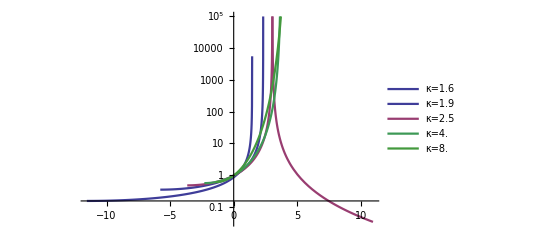

```mathematica
Show[Table[LogPlot[Legended[aNegkappaPlusOneHalf[x,κ,α,vb,T],StringForm["κ=`1`",NumberForm[κ,2]]],{x,-vbprime[vb,T,κ],3*vbprime[vb,T,κ]},PlotStyle->ColorData[1][κ],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic]],{κ,{1.6,1.9,2.5,4.0,8.0}}]]
```

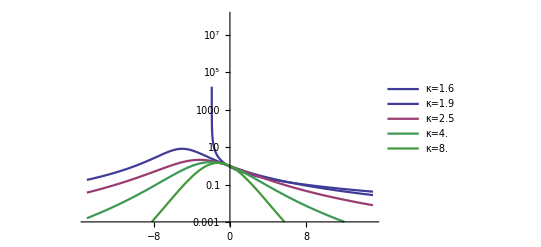

```mathematica
xmin=-15;xmax=15;ymin=10*^-4;ymax=10*^7;
Show[Table[LogPlot[Legended[aNegkappaPlusOneHalf[x,κ,α,vb,T],StringForm["κ=`1`",NumberForm[κ,2]]],{x,xmin,xmax},PlotStyle->ColorData[1][κ],PlotRange->{{xmin,xmax},{ymin,ymax}},PlotLegends->LineLegend[Automatic]],{κ,{1.6,1.9,2.5,4.0,8.0}}]]
```

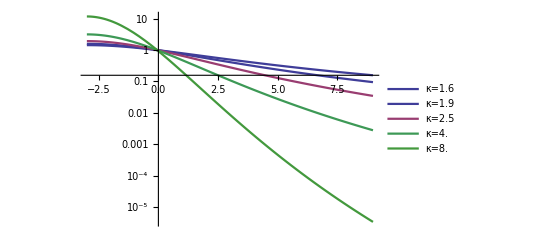
The originalsk plot:
-Graphics-

### Numerically integrate the first term

```mathematica
(*Table[NIntegrate[aNegkappaPlusOneHalf[x,κ,α,vb,T],{x,vbprime[vb,T,κ],∞}],{κ,kappaList}]*)
```

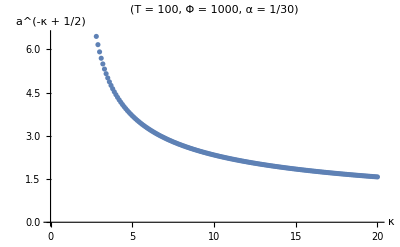

```mathematica
ListPlot[Table[{κ,NIntegrate[aNegkappaPlusOneHalf[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{"κ",StringForm["a^(-κ + 1/2)"] }]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.95066}. NIntegrate obtained 2987.54+240.702 ⅈ and 2734.36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.42322}. NIntegrate obtained 5442.8+2574.29 ⅈ and 3587.2 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-4.13157}. NIntegrate obtained 51053.5+59792. ⅈ and 64200.3 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

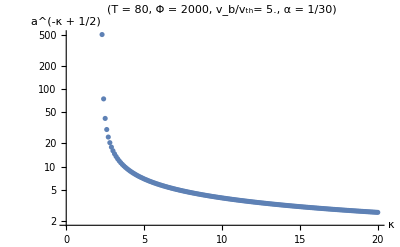

```mathematica
ListLogPlot[Table[{κ,NIntegrate[aNegkappaPlusOneHalf[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{"κ",StringForm["a^(-κ + 1/2)"] }]
```

### Numerically integrate the second term, multiply by eta coefficient

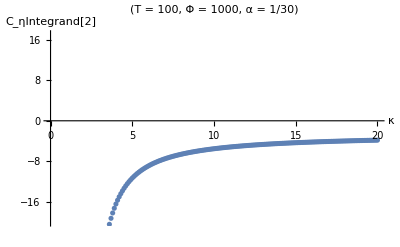

```mathematica
ListPlot[Table[{κ,etaCoeff[κ,α,vb,T]* NIntegrate[etaintegrand2[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{"κ",StringForm["C_ηIntegrand[2]"]},PlotRange->{Automatic,{-20,17}}]
```

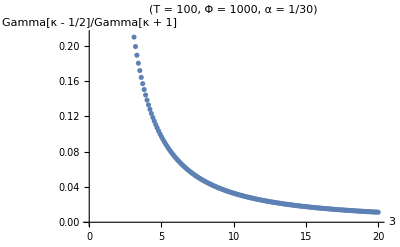

```mathematica
ListPlot[Table[{κ,Gamma[κ-1/2]/Gamma[κ+1]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{κ,StringForm["Gamma[κ - 1/2]/Gamma[κ + 1]"]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.95066}. NIntegrate obtained -12789.3+1035.45 ⅈ and 11762.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-3.42322}. NIntegrate obtained -15578.9+10662.1 ⅈ and 17737.4 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-4.13157}. NIntegrate obtained 143464.+239347. ⅈ and 271867. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

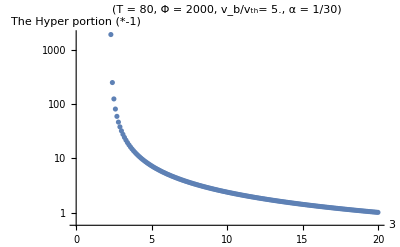

```mathematica
ListLogPlot[Table[{κ,-NIntegrate[etaintegrand2[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{κ,StringForm["The Hyper portion (*-1)"] }]
```

### Numerically integrate the WHOLE THING, multiply by eta coefficient

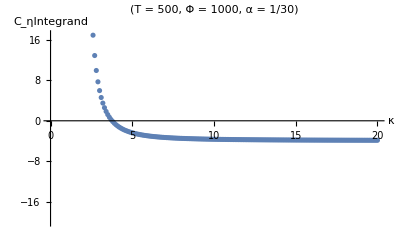

```mathematica
ListPlot[Table[{κ,etaCoeff[κ,α,vb,T]* NIntegrate[etaintegrand[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{"κ",StringForm["C_ηIntegrand"]},PlotRange->{Automatic,{-20,17}}]
```

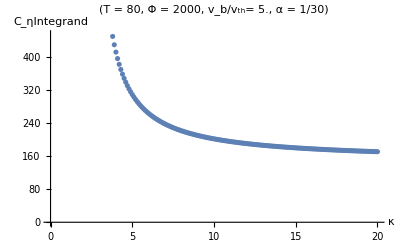

```mathematica
ListPlot[Table[{κ,etaCoeff[κ,α,vb,T]* NIntegrate[etaintegrand[x,κ,α,vb,T],{x,-vbprime[vb,T,κ],∞}]},{κ,kappaList}],PlotLabel->plotParamString,AxesLabel->{"κ",StringForm["C_ηIntegrand"]},PlotRange->{Automatic,Automatic}]
```

### Let’s try κ=20 and see if we can generate the R_B Barbosa curve

```mathematica
kTry=4;
RBList=Range[1.5,99,1.5];
(*tryParamString=StringForm["(T = ``, Φ = ``, κ = ``)",T,pot,kTry];
*)
alphaList=1/x/.x->RBList;
```

```mathematica
alphaList=Range[0.005,0.995,0.005];
```

```mathematica
(*data=Table[{1/alpha,1+etaCoeff[kTry,alpha,vb,T]* NIntegrate[etaintegrand[x,kTry,alpha,vb,T],{x,-vbprime[vb,T,κ],∞}]},{alpha,alphaList}];*)
```

```mathematica
(*data*)
```

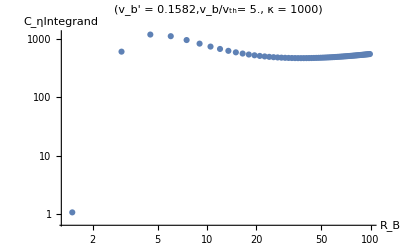

```mathematica
ListLogLogPlot[data,PlotLabel->tryParamString,AxesLabel->{"R_B",StringForm["C_ηIntegrand"]},PlotRange->{Automatic,Automatic}]
```

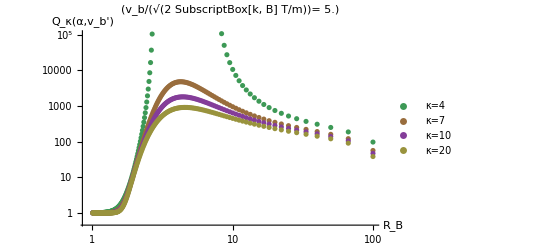

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

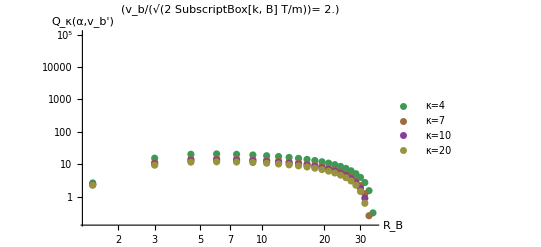

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

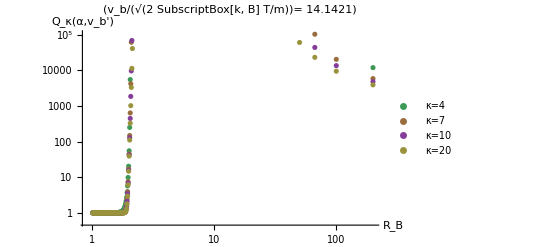

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

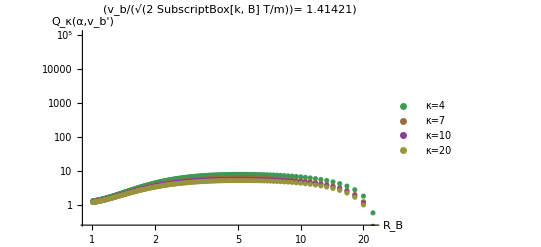

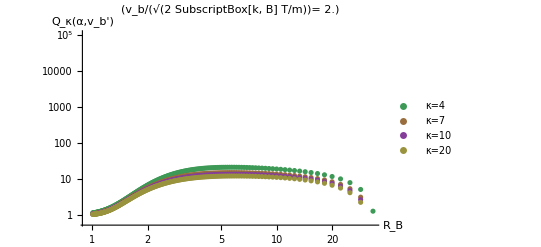

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

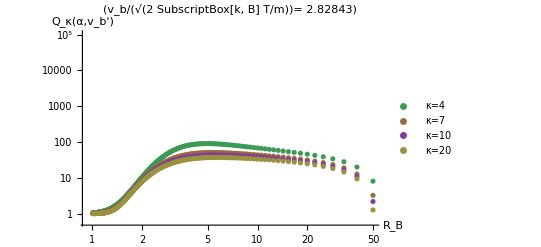

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

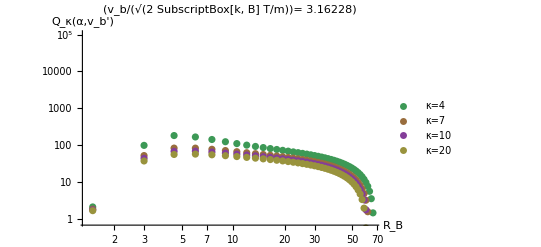

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

-Graphics-

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.8284270130403093318247638255398511102252038338935458678096533093}. NIntegrate obtained 8.79452×10^45 and 3.38002×10^45 for the integral and error estimates.

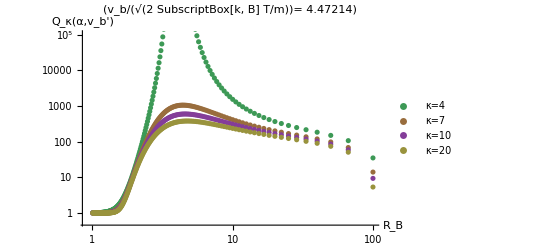

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{All,10*^4},PlotLegends->LineLegend[Automatic],PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,20}}]]
```

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},{1,2*^3 }},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10,30,60}}]]
```

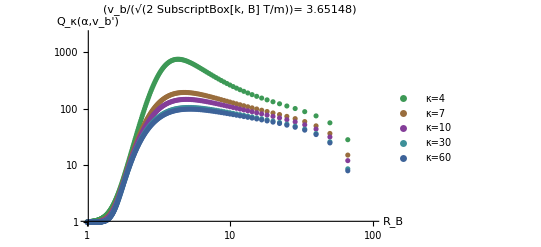

```mathematica
□
```

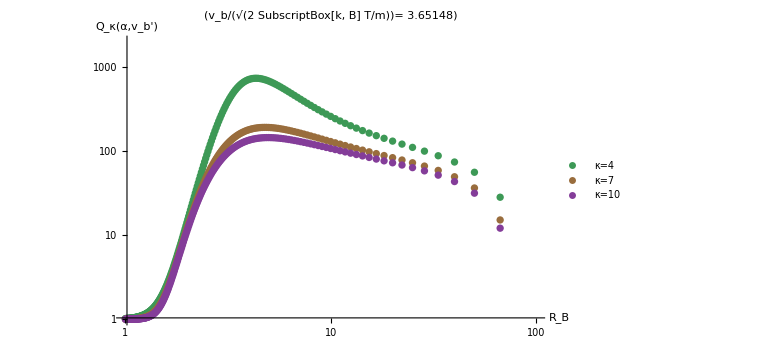

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},{1,2*^3 }},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10}}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {11.7529}. NIntegrate obtained 2.1435+3.50648×10^6 ⅈ and 3.08411×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.82296}. NIntegrate obtained 2.03049+9.9344×10^8 ⅈ and 9.77017×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.17348}. NIntegrate obtained 1.92712+2.7204×10^6 ⅈ and 2.41789×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

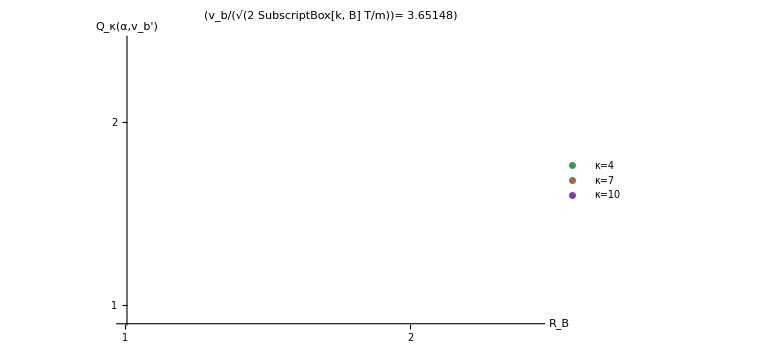

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,1+etaCoeff[k,alpha,vb,T]* NIntegrate[etaintegrand[x,k,alpha,vb,T],{x,-vbprime[vb,T,k],∞}]},{alpha,alphaList}],StringForm["κ=`1`",NumberForm[k,2]]],PlotStyle->ColorData[1][k],PlotRange->{{1,100},Automatic},PlotLegends->LineLegend[Automatic],ImageSize->Large, PlotLabel->tryParamArrString,AxesLabel->{"R_B",StringForm["Q_κ(α,v_b')"]}],{k,{4,7,10}}]]
```